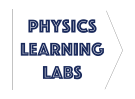
# -Graphics- Lab 9 - Mechanical Resonances

## Background

Mechanical resonances occur in all structures and are important to understand in order to engineer stable and safe buildings and bridges. The Tacoma Narrows Bridge in the great state of Washington collapsed in 1940, four months after it opened. The aerofoil effect, familiar if you blow under a sheet of paper sitting on a table, drove a standing wave resonance between the two towers of this suspension bridge, permitting a large amount of wind energy to be converted to elastic energy as the bridge contorted and ultimately fell.

Different shapes and sizes of material structures can have drastically different resonance structure, or distribution of resonance frequencies. In this quantitative lab, we will explore resonances in three different structures: 
	1) transverse standing waves on a string
	2) radial standing waves on a loop of wire
	3) cantilever resonances in a set of metallic strips.

Recall that a standing wave, or resonance, can have a displacement pattern permitting a harmonic standing wave solution with a well-defined angular wave number k related to the wavelength as

k = (2π)/λ

These wave solutions also have a well-defined angular frequency ω and the frequency f of the wave is related to the period T by

f = 1/T = ω/(2π).

For the standing waves on a string or a suspension bridge, only certain values of k are permitted, since the ends of the string are fixed.

A node (anti-node) is a point on a standing wave where the wave has minimum (maximum) amplitude. For this particular mode of vibration shown in the figure above, there are 4 nodes and 3 anti-nodes. The angular wave number k apparently increases when the number of anti-nodes increases, and so does the frequency. The details of the dependence of wave number on frequency defines the resonance structure and is called the dispersion relation. This dispersion relation depends on material properties like density and any of the many elastic moduli of the material as well as geometry. We will compare below the dispersion relation of waves on a string and waves on a steel loop.

In this lab, the dispersion relations will be measured in three configurations: transverse waves on a stretched string, radial waves on a wire loop, and waves on metal resonance strips.

## Transverse Waves on a Stretched String

If an apparatus is occupied by another lab member, skip to the next resonance experiment.

### Wave Speed and Dispersion Relation

The following figure shows the apparatus for the first part of the lab - waves on a stretched string, which is an example of a standing wave. At one end, a speaker is attached. The speaker is connected to a PASCO Sine Wave Generator which provides the driving frequency to the speaker and hence the string.  At the other end, the string is held under tension by a hanging mass m.

The speed of the wave generated on the string is given by

v = (T/μ)^(1/2),

where T is the tension on the string and μ is the linear density (or mass per unit length) of the string.

The dispersion relation for this special situation in terms of f is

f_n^string=n/(2L)(T/μ)^(1/2),

where L is the length of the string between the point of contact with the speaker and the point of contact with the pulley while n is the number of anti-nodes in the wave generated on the string.

### Experiment

Power on the Pasco 850 Universal Interface , open Lab_9.cap, and navigate to the tab ASDASSD

With the PASCO signal generator, use the coarse and fine FREQUENCY (Hz) knobs to adjust the frequency to locate standing waves frequencies and study the resonances of this simple structure. You can increase or reduce the strength of the vibration with the AMPLITUDE knobs.

Do not adjust the string length or hanging mass in this experiment.

Starting at very low frequency, about 10Hz, increase the FREQUENCY to search for resonance frequencies with different numbers of anti-nodes, n.

Determine and measure the standing wave frequencies for first 5 resonant frequencies. Record the number of anti-nodes (harmonic number) and the frequency as an ordered pair in the list stringdata below. 
For example {{antinodes1, freq1},{antinodes2, freq2}, ... ,{antinodes5, freq5}}.

```mathematica
stringdata={{1,80},{2,161},{3,241},{4,323},{5,404}};
```

```mathematica
stringdata = {{1,22.5},{2,43.5},{3,67.5},{4,89.5},{5,111.5},{6,134.5},{7,157.1}};
```

```mathematica
L=27cm
```

### Plot Fitting

Use the dynamic sliders below to fit your data to a linear function and a quadratic function.  We will continue compare the linear and quadratic plots within the Analysis section.

```mathematica
Manipulate[Show[Plot[{a n,b n^2},{n,0,Max[stringdata[[1;;All,1]]+1]},PlotRange->{{0,All},{0,All}},AxesLabel->{Style["n",Bold],Style["f (Hz)",Bold]},PlotLegends->{"Linear","Quadratic"}],
ListPlot[stringdata,PlotStyle->Red]],
{{a,22.3,"Linear Fit Parameter (slope)"},0,100,0.1,Appearance->"Open"},
{{b,3.3,"Quadratic Fit Parameter"},0,50,0.1,Appearance->"Open"}]
```

## Radial Waves on a Wire Loop

If an apparatus is occupied by another lab member, skip to the next resonance experiment.

### Experiment

Power on the Pasco 850 Universal Interface , open Lab_9.cap, and navigate to the tab ASDASSD

With the PASCO signal generator, use the coarse and fine FREQUENCY (Hz) knobs to adjust the frequency to locate standing waves frequencies and study the resonances of this simple structure. You can increase or reduce the strength of the vibration with the AMPLITUDE knobs.  (be careful w/ amplitude)

Starting at very low frequency, about 10Hz, increase the FREQUENCY to search for resonance frequencies with different numbers of anti-nodes, n.

Determine and measure the standing wave frequencies for 5 different resonances. Record the number of anti-nodes (harmonic number) and the frequency as an ordered pair in the list ringdata below. 
For example {{antinodes1, freq1},{antinodes2, freq2}, ... ,{antinodes5, freq5}}.

```mathematica
ringdata={{3,33},{5,118},{7,250},{9,419},{11,630}};
```

```mathematica
ringdata={{3,31.4},{5,115},{7,243.6},{9,412},{11,619.9}};
```

### Plot Fitting

Use the dynamic sliders to fit your data to a linear function and a quadratic function.  We will continue compare the linear and quadratic plots within the Analysis section.

```mathematica
Manipulate[
Show[Plot[{a n,b n^2},{n,0,Max[ringdata[[1;;All,1]]+1]},PlotRange->{{0,All},{0,All}},AxesLabel->{Style["n",Bold],Style["f (Hz)",Bold]},PlotLegends->{"Linear","Quadratic"}],
ListPlot[ringdata,PlotStyle->Red]],
{{a,48,"Linear Fit Parameter (slope)"},0,100,0.1,Appearance->"Open"},
{{b,5,"Quadratic Fit Parameter"},0,20,0.1,Appearance->"Open"}]
```

## Waves on Metal Resonance Strips

If an apparatus is occupied by another lab member, skip to the next resonance experiment.

### Dispersion Relation and Young’s Modulus

The theoretical frequency of vibration of a cantilever with one end fixed and another free is

-Graphics-

For the materials-specific information, the Young’s modulus E (units N/m^2) measures the stiffness of the material and the density ρ (units kg/m^3) tells us how much matter moves as the beam vibrates. The Young’s modulus of common materials is usually in the range 1-1000 GPa (1 GPa= 10^9 N/m^2).

The coefficients α_1=1.875, α_2=4.694, α_3=7.885 are given from numerical integrals. The deflection patterns and resonant frequencies are shown below.

Rewriting the theoretical expression the lowest frequency mode as

-Graphics-,

note that if you plot the resonance frequency f_1 of the metal strip as a function of its inverse length 1/L^2, we should be able to fit to a line, and the slope will permit us to determine the Young’s modulus E from the density and thickness h.

### Experiment

Power on the Pasco 850 Universal Interface , open Lab_9.cap, and navigate to the tab ASDASSD

With the PASCO signal generator, use the coarse and fine FREQUENCY (Hz) knobs to adjust the frequency to locate standing waves frequencies and study the resonances of this simple structure. You can increase or reduce the strength of the vibration with the AMPLITUDE knobs.

Starting at very low frequency, about 10Hz, increase the FREQUENCY to search for resonance frequencies with different numbers of anti-nodes, n. Choose at least five different values of n and enter your data as ordered pairs below. The number of anti-nodes is the first entry and frequency is the second entry (e.g. {# nodes, frequency in Hertz}).

Enter your data as ordered pairs representing the half length L of the resonance strip (see figure below) in the first entry and frequency in the second entry (e.g. {length in m, frequency in Hertz}).

Measure the geometrical information h and w with calipers and enter them into the corresponding variables below. Units are meters.

```mathematica
coef=1.875^2/(2π)
```

0.559529

```mathematica
number=0.1615;
w=0.01;
h=0.00068;
```

The longest strip was weighed and it was determined to be 9.5g. This line of code calculates the density in kg/m^3 for your strip from this information.

```mathematica
density=0.0095/(w h 0.19) (*the weight of the longest strip is 9.5g and its length is 19cm*)
```

7352.94

Starting at very low frequency, about 10Hz, increase the FREQUENCY to search for the lowest resonance frequency for each strip length.

Determine and measure the lowest resonant frequency for each strip length. Record the strip length (in meters) and the frequency as an ordered pair in the list stripdata below. 
For example {{length1, freq1},{length2, freq2},{length3, freq3}}.

```mathematica
stripdata={{0.19,69},{0.16,96},{0.13,149}};
```

```mathematica
stripdata = {{0.19/2,69},{0.16/2,97.8},{0.13/2,147.5}};
```

```mathematica
stripdata*2
```

{{0.191,138},{0.16,195.6},{0.1304,295.}}

### Plot Fitting

Since we have only measured the lowest frequency of vibration, we will not plot f(n) as with the string and radial waves. Instead, we will plot the frequencies as a function of L^-2. The resulting plot will allow us to determine the modulus of elasticity E of the strip material.

Use the dynamic sliders to fit your data to a linear function and a quadratic function.  We utilize the slope and continue to calculate E within the Analysis section.

```mathematica
Manipulate[
Show[Plot[a x,{x,0,1.1/(Min[stripdata[[1;;All,1]]])^2},PlotRange->{{0,All},{0,All}},AxesLabel->{Style["L^-2 (m)",Bold],Style["f (Hz)",Bold]}],
ListPlot[Table[{1/(stripdata[[i,1]])^2,stripdata[[i,2]]},{i,1,Length[stripdata]}],PlotStyle->Red]],
{{a,0.62,"Linear Fit Parameter (slope)"},0,10,0.01,Appearance->"Open"}]
```

## Analysis

### Transverse Waves on a Stretched String

Which fit is more appropriate for the data, linear or quadratic?

From your data and fit, find the mass per unit length μ of the string. Is this reasonable? Why?

### Radial Waves on a Wire Loop

Discuss how this is different from transverse waves on a stretched spring.

### Waves on Metal Resonance Strips

If you double the length of a string, the period of the lowest frequency standing wave doubles.
If you double the length of a cantilever, the period of the lowest frequency standing wave ______.

Discuss how the frequency of the cantilever depends on geometric information L, w, and h.

Now use the slope s, the density ρSteel, the strip width w and strip thickness h to find the Young’s modulus E.

Use the following chart to determine the strip material

What material would give a higher vibrational frequency than your strips? Why?

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).